```mathematica
$Assumptions = {μ1 ∈ Reals, μ2 ∈ Reals, μ3 ∈Reals, ΓL ∈ Reals, ΓR ∈ Reals, t1 ∈ Reals, t2 ∈ Reals, Δ1 ∈Reals, Δ2 ∈ Reals, 0≤ϕ≤ 2*Pi, ω∈Reals}
```

{μ1∈ℝ,μ2∈ℝ,μ3∈ℝ,ΓL∈ℝ,ΓR∈ℝ,t1∈ℝ,t2∈ℝ,Δ1∈ℝ,Δ2∈ℝ,0≤ϕ≤2 π,ω∈ℝ}

```mathematica
W[ΓL_, ΓR_]:= DiagonalMatrix[{Sqrt[ΓL],0,Sqrt[ΓR],-Sqrt[ΓL],0,-Sqrt[ΓR]}];
```

```mathematica
H[μ1_,μ2_,μ3_,t1_,t2_,Δ1_, Δ2_, ϕ_]:={
{μ1, t1, 0, 0, -Δ1,0}, {t1, μ2, t2, Δ1,0,-Δ2*Exp[I*ϕ]}, {0,t2,0.3 μ3, 0, Δ2*Exp[I*ϕ],0},{0, Δ1, 0, -μ1, -t1,0}, {-Δ1,0,Δ2*Exp[-I*ϕ], -t1, -μ2, -t2},{0, -Δ2*Exp[-I*ϕ],0,0,-t2,-0.3 μ3}
};
```

```mathematica
S[H_,W_, ω_]:= IdentityMatrix[6] - I*Transpose[W].Inverse[ω*IdentityMatrix[6] - H + (I/2)*W.Transpose[W]].W ;
```

```mathematica
G0LL[H_,W_, ω_]:=Module[{Smat},Smat=S[H,W,ω]; 1-Abs[Smat[[1,1]]]^2+Abs[Smat[[4,1]]]^2];
```

```mathematica
GTLL[G0LL_,H_,W_,T_,ω_]:=Module[{integrand},integrand[ε_]:=G0LL[H,W,ε]/(4 T Cosh[(ε-ω)/(2 T)]^2);
NIntegrate[integrand[ε],{ε,-120,120}]]
```

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0., ϕ=0}, Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]]]
```

0.352458

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0.}, Table[Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]], {ϕ, {0, 0.5, 1, 1.5, 2, 2.5, Pi, 3.5, 4, 4.5, 5. , 6., 2 Pi}}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {6.09002}. NIntegrate obtained 0.516747+0. ⅈ and 8.61639×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-3.28498}. NIntegrate obtained 0.596368+0. ⅈ and 9.96775×10^-7 for the integral and error estimates.

{0.352458,0.353363,0.357056,0.368372,0.405424,0.516747,0.00850789,0.596368,0.455791,0.383872,0.36188,0.352734,0.352458}

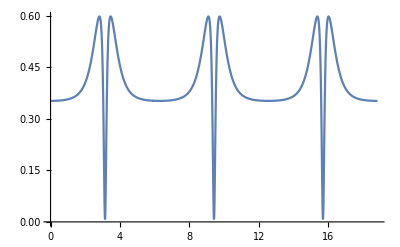

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0.}, Plot[Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]], {ϕ, 0, 6 Pi}]]
```

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0.}, (1/(2 Pi)) NIntegrate[Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]], {ϕ, 0, 2 Pi}]]
```

NIntegrate::inumr: The integrand 0.0833333 (1+Abs[0.+1.22474 (0.+Times[«3»])]^2-Abs[1-ⅈ Plus[«2»]]^2) Sech[0.166667 (0.+ε)]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-30,30}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.402873

```mathematica
n = 50;
ϕrange = Subdivide[0, 2 Pi, n];
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0.}, Mean[Table[Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]], {ϕ, ϕrange}]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-5.62873}. NIntegrate obtained 0.521012+0. ⅈ and 1.3975×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-4.69123}. NIntegrate obtained 0.561792+0. ⅈ and 5.86268×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {3.74627}. NIntegrate obtained 0.593814+0. ⅈ and 2.23017×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.401547

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-59.535}. NIntegrate obtained 3.22194×10^-8+0. ⅈ and 5.25774×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-59.535}. NIntegrate obtained 4.18302×10^-8+0. ⅈ and 7.70752×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-59.535}. NIntegrate obtained 6.50011×10^-8+0. ⅈ and 1.04172×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

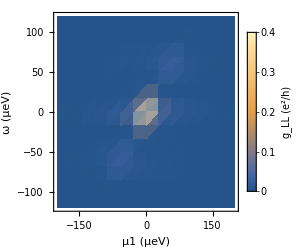

```mathematica
ChargeStabDiagFirstQD =  With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ2=0., μ3=0.}, DensityPlot[Mean[Table[Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {μ1, -200, 200}, {ω, -120, 120},ImageSize->250,
FrameLabel->{Style["μ1 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,LL]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

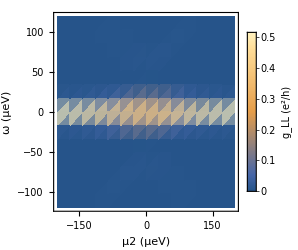

ChargeStabDiagSecondQD.pdf

```mathematica
ChargeStabDiagSecondQD = With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ1=0., μ3=0.}, DensityPlot[Mean[Table[Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {μ2, -200, 200}, {ω, -120, 120},ImageSize->250,
FrameLabel->{Style["μ2 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,LL]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-84.8475}. NIntegrate obtained 4.34982×10^-8+0. ⅈ and 1.02811×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-84.8475}. NIntegrate obtained 5.20677×10^-8+0. ⅈ and 4.34043×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-84.8475}. NIntegrate obtained 6.62626×10^-8+0. ⅈ and 4.75608×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

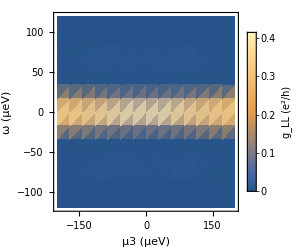

```mathematica
ChargeStabDiagThirdQD=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ1=0., μ2=0.}, DensityPlot[Mean[Table[Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {μ3, -200, 200}, {ω, -120, 120},ImageSize->250,
FrameLabel->{Style["μ3 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,LL]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

```mathematica
Export["ChargeStabDiagThirdQD.pdf", ChargeStabDiagThirdQD, ImageResolution -> 600]
```

ChargeStabDiagThirdQD.pdf

```mathematica
Export["ChargeStabDiagFirstQD.pdf", ChargeStabDiagFirstQD, ImageResolution->600]
```

ChargeStabDiagFirstQD.pdf

```mathematica
Export["ChargeStabDiagSecondQD.pdf", ChargeStabDiagSecondQD, ImageResolution->600]
```

ChargeStabDiagSecondQD.pdf

```mathematica
Export["ChargeStabDiagThirdQD.pdf", ChargeStabDiagThirdQD, ImageResolution->600]
```

ChargeStabDiagThirdQD.pdf

```mathematica
GLLPLots = GraphicsGrid[{{ChargeStabDiagFirstQD,ChargeStabDiagSecondQD,ChargeStabDiagThirdQD}},Spacings->{0.,0.},Alignment->Center, ImageSize->{1080,360}]
```

-Graphics-

```mathematica
Export["GLLPLots.pdf", GLLPLots, ImageResolution->600]
```

GLLPLots.pdf

```mathematica
Export["GLLQD1.pdf", ChargeStabDiagFirstQD, ImageResolution->600]
```

GLLQD1.pdf

```mathematica
Export["GLLQD2.pdf", ChargeStabDiagSecondQD, ImageResolution->600]
```

GLLQD2.pdf

```mathematica
Export["GLLQD3.pdf", ChargeStabDiagThirdQD, ImageResolution->600]
```

GLLQD3.pdf

```mathematica
G0RR[H_,W_, ω_]:=Module[{Smat},Smat=S[H,W,ω]; 1-Abs[Smat[[3,3]]]^2+Abs[Smat[[6,3]]]^2];
GTRR[G0RR_,H_,W_,T_,ω_]:=Module[{integrand},integrand[ε_]:=G0RR[H,W,ε]/(4 T Cosh[(ε-ω)/(2 T)]^2);
NIntegrate[integrand[ε],{ε,-120,120}]]
```

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0., ϕ=0}, Chop[GTRR[G0RR,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-0.00372999}. NIntegrate obtained 0.0764809+0. ⅈ and 0.0000281704 for the integral and error estimates.

0.0764809

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0.}, Table[Chop[GTRR[G0RR,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]], {ϕ, {0, 0.5, 1, 1.5, 2, 2.5, Pi, 3.5, 4, 4.5, 5. , 6., 2 Pi}}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-0.00372999}. NIntegrate obtained 0.0764809+0. ⅈ and 0.0000281704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {0.46502}. NIntegrate obtained 0.0764855+0. ⅈ and 0.0000288557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {0.46502}. NIntegrate obtained 0.0765142+0. ⅈ and 0.0000395646 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0764809,0.0764855,0.0765142,0.0766575,0.0772504,0.0794981,0.0782325,0.0818525,0.0782026,0.0768875,0.0765718,0.0764823,0.0764809}

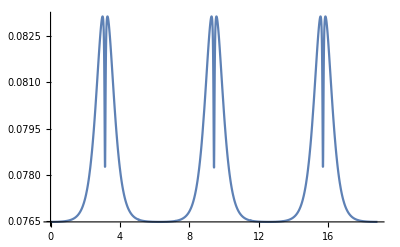

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0.}, Plot[Chop[GTRR[G0RR,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]], {ϕ, 0, 6 Pi}]]
```

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0.}, (1/(2 Pi)) NIntegrate[Chop[GTRR[G0RR,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]], {ϕ, 0, 2 Pi}]]
```

0.0778682

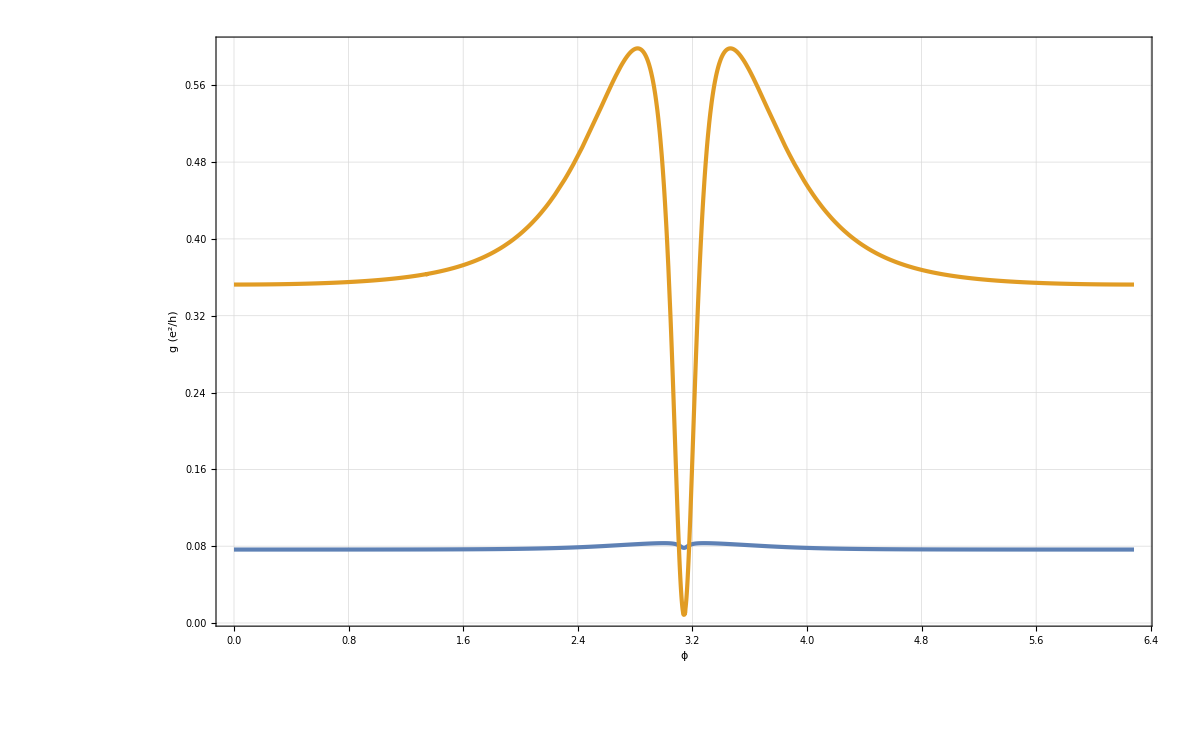

```mathematica
gvsphase = With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,ω=0.,T=3.,μ1=0.,μ2=0., μ3=0.}, Plot[{Chop[GTRR[G0RR,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]],Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR], T,ω]]}, {ϕ,0,2 Pi}, 
(*stile curve*)PlotStyle->{Directive[AbsoluteThickness[3]],Directive[AbsoluteThickness[3]]},
(*etichette assi*)Frame->True,Axes->False,FrameLabel->{Style["ϕ",28],Style[Row[{g," (",TraditionalForm[e^2/h],")"}], 36]},
(*stile ticks*)FrameTicksStyle->Directive[Black,40],
(*dimensioni*)ImageSize->1200,
(*padding per evitare tagli*)ImagePadding->{{180,20},{100,20}},
(*griglia leggera*)GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]],
(*range automatico ma ordinato*)PlotRange->All,
(*sfondo bianco*)Background->White,
(*font globale*)BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
]
```

```mathematica
Export["cond_vs_phase.pdf", gvsphase, ImageResolution->600]
```

cond_vs_phase.pdf

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-59.535}. NIntegrate obtained 2.3532×10^-7+0. ⅈ and 7.2929×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-60.0037}. NIntegrate obtained 2.35776×10^-7+0. ⅈ and 7.23156×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-60.0037}. NIntegrate obtained 2.37137×10^-7+0. ⅈ and 6.27712×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

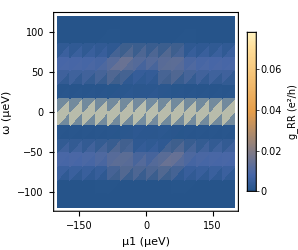

```mathematica
GRRQD1=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ2=0., μ3=0.}, DensityPlot[Mean[Table[Chop[GTRR[G0RR,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {μ1, -200, 200}, {ω, -120, 120},ImageSize->250,
FrameLabel->{Style["μ1 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,RR]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

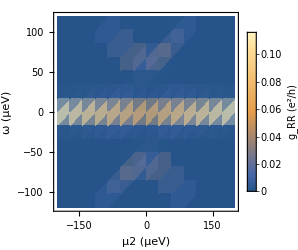

```mathematica
GRRQD2=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ1=0., μ3=0.}, DensityPlot[Mean[Table[Chop[GTRR[G0RR,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {μ2, -200, 200}, {ω, -120, 120},ImageSize->250,
FrameLabel->{Style["μ2 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,RR]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-84.8475}. NIntegrate obtained 8.40796×10^-7+0. ⅈ and 3.10987×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-84.8475}. NIntegrate obtained 8.46305×10^-7+0. ⅈ and 3.18085×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-84.8475}. NIntegrate obtained 8.6277×10^-7+0. ⅈ and 3.4761×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

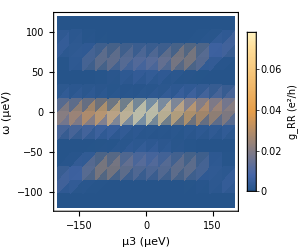

```mathematica
GRRQD3=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ1=0., μ2=0.}, DensityPlot[Mean[Table[Chop[GTRR[G0RR,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {μ3, -200, 200}, {ω, -120, 120},ImageSize->250,
FrameLabel->{Style["μ3 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,RR]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

```mathematica
GRRPlots = GraphicsGrid[{{GRRQD1, GRRQD2, GRRQD3}},Spacings->{0.,0.},Alignment->Center, ImageSize->{1080,360}]
```

-Graphics-

```mathematica
Export["GRRPlots.pdf", GRRPlots, ImageResolution->600]
```

GRRPlots.pdf

```mathematica
Export["GRRQD1.pdf", GRRQD1, ImageResolution->600]
```

GRRQD1.pdf

```mathematica
Export["GRRQD2.pdf", GRRQD2, ImageResolution->600]
```

GRRQD2.pdf

```mathematica
Export["GRRQD3.pdf", GRRQD3, ImageResolution->600]
```

GRRQD3.pdf

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-103.129}. NIntegrate obtained 0.00584654+0. ⅈ and 9.9617×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-103.129}. NIntegrate obtained 0.00583984+0. ⅈ and 1.19778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-103.129}. NIntegrate obtained 0.00581982+0. ⅈ and 4.49094×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

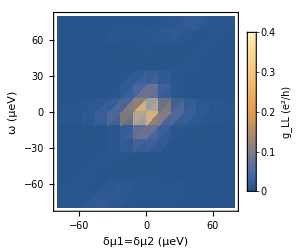

```mathematica
StabilityQD1QD2=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3., μ3=0.}, DensityPlot[Mean[Table[Chop[GTLL[G0LL,H[δ,δ,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {δ, -80, 80}, {ω, -80, 80},ImageSize->250,
FrameLabel->{Style["δμ1=δμ2 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,LL]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-104.066}. NIntegrate obtained 0.00669802+0. ⅈ and 8.33552×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-104.066}. NIntegrate obtained 0.00669116+0. ⅈ and 1.45913×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-104.066}. NIntegrate obtained 0.00667062+0. ⅈ and 7.03216×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

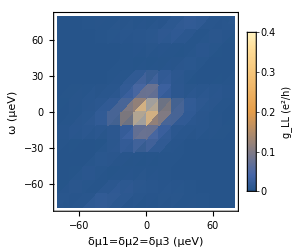

```mathematica
StabilityQD1QD2QD3=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.}, DensityPlot[Mean[Table[Chop[GTLL[G0LL,H[δ,δ,δ,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {δ, -80, 80}, {ω, -80, 80},ImageSize->250,
FrameLabel->{Style["δμ1=δμ2=δμ3 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,LL]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-90.4725}. NIntegrate obtained 0.00102124+0. ⅈ and 1.76333×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-90.4725}. NIntegrate obtained 0.00102124+0. ⅈ and 1.76262×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-90.4725}. NIntegrate obtained 0.00102124+0. ⅈ and 1.76053×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

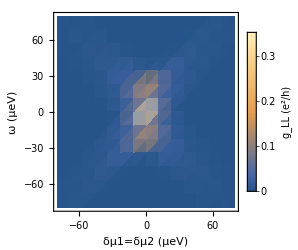

```mathematica
StabilityQD3OffRes=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3., μ3=5000.}, DensityPlot[Mean[Table[Chop[GTLL[G0LL,H[δ,δ,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {δ, -80, 80}, {ω, -80, 80},ImageSize->250,
FrameLabel->{Style["δμ1=δμ2 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,LL]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

```mathematica
StabilityPlots = GraphicsGrid[{{StabilityQD3OffRes, StabilityQD1QD2, StabilityQD1QD2QD3}},Spacings->{0.,0.},Alignment->Center, ImageSize->{1080,360}]
```

-Graphics-

```mathematica
Export["StabilityPlots.pdf", StabilityPlots, ImageResolution->600]
```

```mathematica
"StabilityPlots.pdf"
```

```mathematica
Export["StabilityQD1QD2.pdf", StabilityQD1QD2, ImageResolution->600]
```

StabilityQD1QD2.pdf

```mathematica
Export["StabilityQD1QD2QD3.pdf", StabilityQD1QD2QD3, ImageResolution->600]
```

StabilityQD1QD2QD3.pdf

```mathematica
Export["StabilityQD3OffRes.pdf", StabilityQD3OffRes, ImageResolution->600]
```

StabilityQD3OffRes.pdf

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-103.129}. NIntegrate obtained 0.00288945+0. ⅈ and 5.21826×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-103.129}. NIntegrate obtained 0.00288544+0. ⅈ and 6.36709×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-103.129}. NIntegrate obtained 0.00287344+0. ⅈ and 2.47213×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

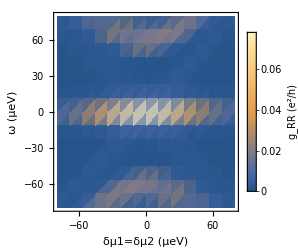

```mathematica
StabilityGRRQD1QD2=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3., μ3=0.}, DensityPlot[Mean[Table[Chop[GTRR[G0RR,H[δ,δ,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {δ, -80, 80}, {ω, -80, 80},ImageSize->250,
FrameLabel->{Style["δμ1=δμ2 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,RR]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-104.066}. NIntegrate obtained 0.00517343+0. ⅈ and 6.49472×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-104.066}. NIntegrate obtained 0.00516737+0. ⅈ and 1.10602×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-104.066}. NIntegrate obtained 0.0051492+0. ⅈ and 5.48788×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

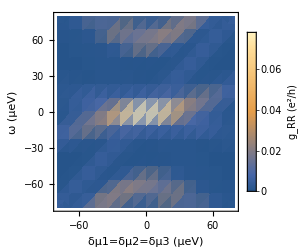

```mathematica
StabilityGRRQD1QD2QD3=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.}, DensityPlot[Mean[Table[Chop[GTRR[G0RR,H[δ,δ,δ,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {δ, -80, 80}, {ω, -80, 80},ImageSize->250,
FrameLabel->{Style["δμ1=δμ2=δμ3 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,RR]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-70.3162}. NIntegrate obtained 9.50327×10^-6+0. ⅈ and 1.63267×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-70.3162}. NIntegrate obtained 9.50202×10^-6+0. ⅈ and 1.63188×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-70.3162}. NIntegrate obtained 9.49828×10^-6+0. ⅈ and 1.62952×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

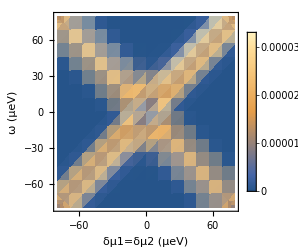

```mathematica
StabilityGRRQD3OffRes=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ3=5000.}, DensityPlot[Mean[Table[Chop[GTRR[G0RR,H[δ,δ,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {δ, -80, 80}, {ω, -80, 80},ImageSize->250,
FrameLabel->{Style["δμ1=δμ2 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,RR]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-100.785}. NIntegrate obtained 0.000051376+0. ⅈ and 9.67613×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-100.785}. NIntegrate obtained 0.0000513756+0. ⅈ and 9.67513×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-100.785}. NIntegrate obtained 0.0000513744+0. ⅈ and 9.67217×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

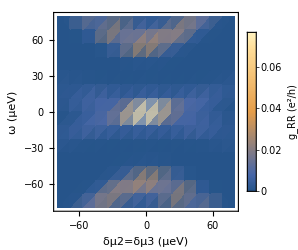

```mathematica
StabilityGRRQD1OffRes=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ1=5000.}, DensityPlot[Mean[Table[Chop[GTRR[G0RR,H[μ1,δ,δ,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {δ, -80, 80}, {ω, -80, 80},ImageSize->250,
FrameLabel->{Style["δμ2=δμ3 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,RR]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-102.191}. NIntegrate obtained 0.0000483929+0. ⅈ and 7.16204×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-102.191}. NIntegrate obtained 0.0000485992+0. ⅈ and 7.80531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-102.191}. NIntegrate obtained 0.0000487869+0. ⅈ and 8.60179×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

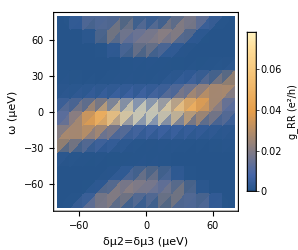

```mathematica
StabilityGRRQD2QD3=With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,μ1=0.}, DensityPlot[Mean[Table[Chop[GTRR[G0RR,H[μ1,δ,δ,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {δ, -80, 80}, {ω, -80, 80},ImageSize->250,
FrameLabel->{Style["δμ2=δμ3 (μeV)", 12],Style["ω (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,RR]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```

```mathematica
StabilityPlotsGRR = GraphicsGrid[{{StabilityGRRQD1OffRes, StabilityGRRQD2QD3, StabilityGRRQD1QD2QD3}},Spacings->{0.,0.},Alignment->Center, ImageSize->{1080,360}]
```

-Graphics-

```mathematica
Export["StabilityPlotsGRR.pdf", StabilityPlotsGRR, ImageResolution->600]
```

StabilityPlotsGRR.pdf

```mathematica
Export["StabilityGRRQD1OffRes.pdf", StabilityGRRQD1OffRes, ImageResolution->600]
```

StabilityGRRQD1OffRes.pdf

```mathematica
Export["StabilityGRRQD2QD3.pdf", StabilityGRRQD2QD3, ImageResolution->600]
```

StabilityGRRQD2QD3.pdf

```mathematica
Export["StabilityGRRQD1QD2QD3.pdf", StabilityGRRQD1QD2QD3, ImageResolution->600]
```

StabilityGRRQD1QD2QD3.pdf

```mathematica
With[{t1=10.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3., μ3=5000., μ1=40., μ2=40.}, 
data=Table[{ω,Mean@Table[Chop@GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1,Δ2,ϕ],W[ΓL,ΓR],T,ω],{ϕ,ϕrange}]},{ω,-80,80,0.5}]];
```

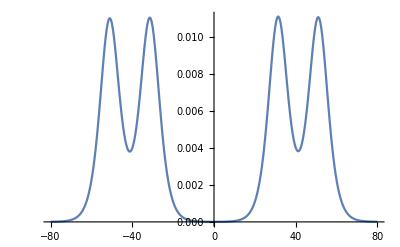

```mathematica
ListLinePlot[data,PlotRange->All]
```

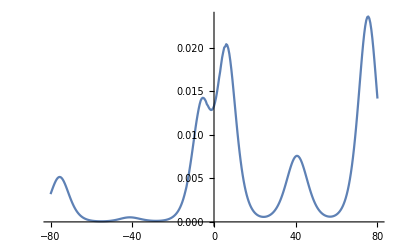

```mathematica
allthree = data;
```

```mathematica
justtwo = data;
```

```mathematica
thirdoffres = data;
```

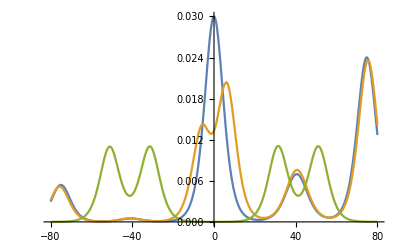

```mathematica
ListLinePlot[{justtwo, allthree, thirdoffres}, PlotRange->All]
```

```mathematica
plot=ListLinePlot[{justtwo,allthree, thirdoffres},
(*stile curve*)PlotStyle->{Directive[Blue, AbsoluteThickness[3]],Directive[Red,AbsoluteThickness[3]], Directive[RGBColor["#00802b"], AbsoluteThickness[3]]},
(*etichette assi*)Frame->True,Axes->False,FrameLabel->{Style["ω (μeV)",36],Style[Row[{Subscript[g,L]," (",TraditionalForm[e^2/h],")"}], 36]},
(*stile ticks*)FrameTicksStyle->Directive[Black,40],
(*legenda*)PlotLegends->Placed[{"Two sites detuning","Three sites detuning", "QD3 off res"},{0.25,0.80}],
(*dimensioni*)ImageSize->1200,
(*padding per evitare tagli*)ImagePadding->{{220,20},{100,20}},
(*griglia leggera*)GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]],
(*range automatico ma ordinato*)PlotRange->All,
(*sfondo bianco*)Background->White,
(*font globale*)BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->28}];
```

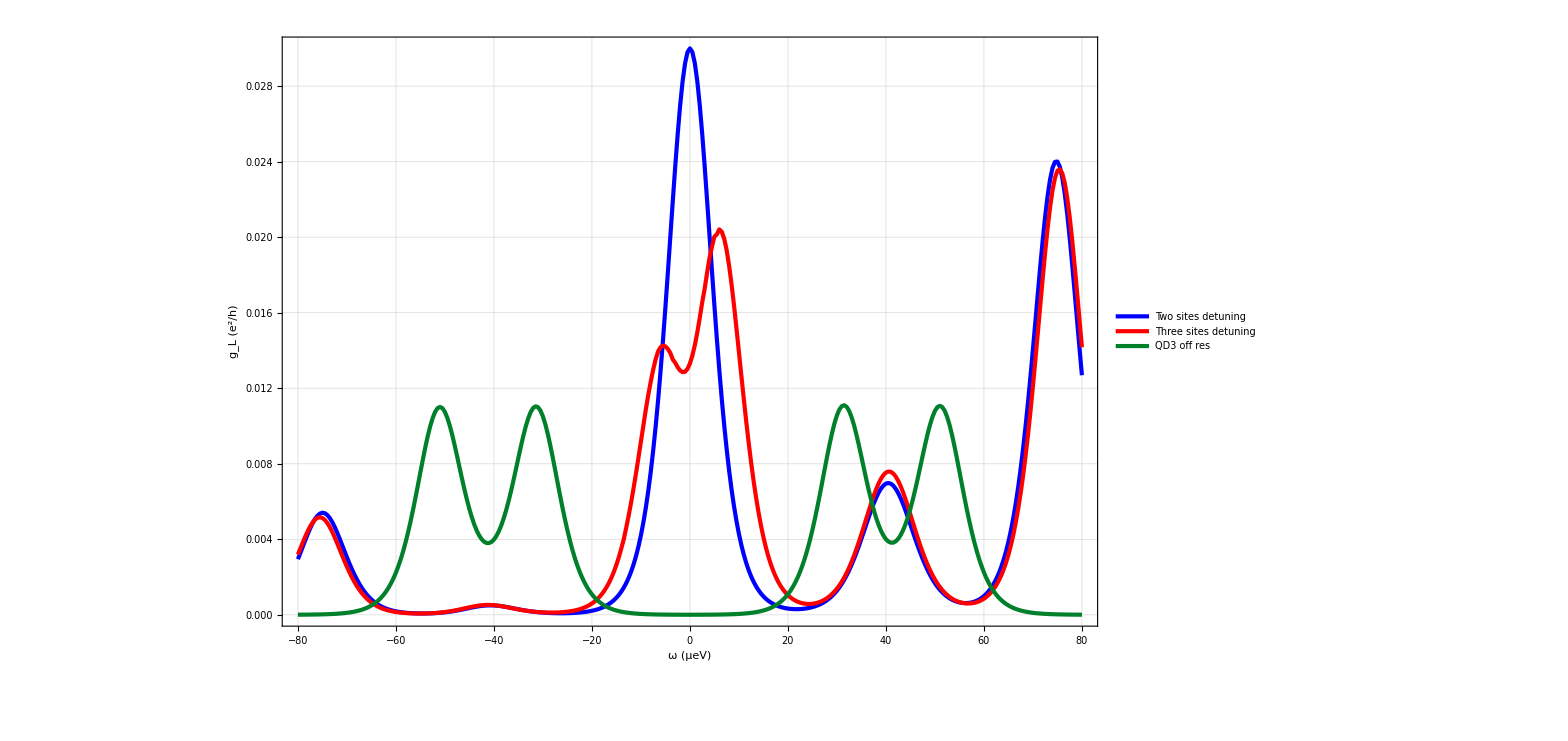

```mathematica
plot
```

```mathematica
Export["line_cuts_stability.pdf",plot,ImageResolution->600]
```

line_cuts_stability.pdf

```mathematica
Directory[]
```

C:\Users\Tullio\Documents

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-13.1287}. NIntegrate obtained 0.00360899+0. ⅈ and 2.07612×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-13.1287}. NIntegrate obtained 0.00360894+0. ⅈ and 2.07549×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ε near {ε} = {-13.1287}. NIntegrate obtained 0.00360879+0. ⅈ and 2.07359×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

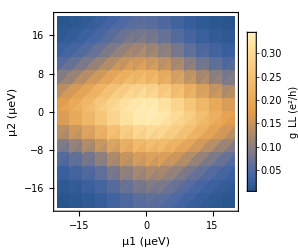

```mathematica
ChargeStabDiagQD3OffRes =  With[{t1=9.,Δ1=10.,t2=30., Δ2=30.,ΓL=1.5,ΓR=0.3,T=3.,ω=0., μ3=5000.}, DensityPlot[Mean[Table[Chop[GTLL[G0LL,H[μ1,μ2,μ3,t1,t2,Δ1, Δ2, ϕ],W[ΓL, ΓR],T,ω]], {ϕ, ϕrange}]], {μ1, -20, 20}, {μ2, -20, 20},ImageSize->250,
FrameLabel->{Style["μ1 (μeV)", 12],Style["μ2 (μeV)", 12]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
FrameStyle->Directive[Black,Thick],
ImagePadding->All,
FrameTicksStyle->Directive[Black,13],
PlotRange->All,
PlotTheme->"Detailed", PlotLegends ->BarLegend[Automatic, LegendLabel->Style[Row[{Subscript[g,LL]," (",TraditionalForm[e^2/h],")"}], 12], LabelStyle->Directive[12]]
]]
```